## Branching Model of Leafs

### Basic Model

number of branches

length of branches

angle of branches

number of branching

### Extension

Ways of “connecting” the end-points

no connections (e.g. ferns??)

straight line

spider web (bent inward, what rounding)

bent outwards, what rounding?

## Implementation

### End Points

The first line is assumed to be from {-1,0} to {0,0}
b is a list of points specified as complex numbers
n is the depth of the branching

```mathematica
points[b_,n_]:=NestList[Flatten[Outer[Times,1+#,b]]&,{0},n]
```

The function returns a nested list where each sublist is a new layer in the depth of the tree

```mathematica
points[{0.7+0.1I,0.7-0.1I},2]
```

{{0},{0.7+0.1 ⅈ,0.7-0.1 ⅈ},{1.18+0.24 ⅈ,1.2-0.1 ⅈ,1.2+0.1 ⅈ,1.18-0.24 ⅈ}}

Basic visualization of the points:

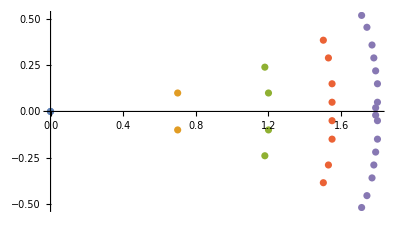

```mathematica
ComplexListPlot[points[{0.7+0.1I,0.7-0.1I},4]]
```

In : {{a}, {b, c}, {d, e, f, g}}
Out : {a,b}, {a,c}, {b,d}, {b,f}, {c,e}, {c,g}

### Visualization

```mathematica
basicLeaf[b_, n_] := 
	Module[{nBranch,nestedPoints,lines},
		nBranch= Length[b];
		nestedPoints= NestList[Flatten[Outer[Times,1+#,b]]&,{0},n];
		lines=Flatten[MapIndexed[
			Table[
				Table[
					{#1[[x]],nestedPoints[[#2[[1]]+1]][[(x+(y-1)*Length[#1])]]},
					{y,nBranch}],
				{x,Length[#1]}]&,
			Most[nestedPoints]],2];
		Graphics[Line[Map[Reverse,ReIm[lines],2]]]]
```

```mathematica
NestedBranching[b_, n_,OptionsPattern["Output"->"Graphic"]] :=
	Module[{nBranch,nestedPoints,lines},
		nBranch= Length[b];
		nestedPoints= NestList[Flatten[Outer[Times,1+#,b]]&,{0},n];
		lines=Flatten[MapIndexed[
			Table[
				Table[
					{#1[[x]],nestedPoints[[#2[[1]]+1]][[(x+(y-1)*Length[#1])]]},
					{y,nBranch}],
				{x,Length[#1]}]&,
			Most[nestedPoints]],2];
		If[
			OptionValue["Output"]=="Points",
			nestedPoints,
			If[
				OptionValue["Output"]=="EndPoints",
				Last[nestedPoints],
				If[
					OptionValue["Output"]=="Lines",
					lines,
					If[
						OptionValue["Output"]=="Graphic",
						Graphics[Line[Map[Reverse,ReIm[Join[{{-1,0}},lines]],2]]]]]]]]
```

```mathematica
points[{0.7+0.2I,0.7-0.2I},2]
```

{{0},{0.7+0.2 ⅈ,0.7-0.2 ⅈ},{1.15+0.48 ⅈ,1.23-0.2 ⅈ,1.23+0.2 ⅈ,1.15-0.48 ⅈ}}

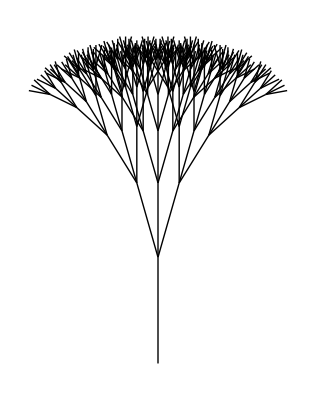

```mathematica
NestedBranching[{0.7+0.2I,0.7,0.7-0.2I},5]
```

## Sandbox :D

```mathematica
visualization[b_,n_]:=
Module[{points},
points =Catenate[Reap[NestList[Sow[{#,Flatten[Outer[Times,1+#,b]]}][[2]]&,{0},n]][[2]]];
points]
```

```mathematica
visualization[{0.7+0.1I,0.7-0.1I},2]
```

{{{{0},{0.7+0.1 ⅈ,0.7-0.1 ⅈ}},{{0.7+0.1 ⅈ,0.7-0.1 ⅈ},{1.18+0.24 ⅈ,1.2-0.1 ⅈ,1.2+0.1 ⅈ,1.18-0.24 ⅈ}}}}

```mathematica
generators={0.8+0.15I,0.8-0.1I}
```

{0.8+0.15 ⅈ,0.8-0.1 ⅈ}

```mathematica
points={1}
```

{1}

```mathematica
Reap[Catenate[Map[Sow[{#,#*generators}][[2]]&,points]]]
```

{{0.7+0.1 ⅈ,0.7-0.1 ⅈ},{{{1,{0.7+0.1 ⅈ,0.7-0.1 ⅈ}}}}}

```mathematica
nestedPoints =Reap[Nest[Catenate[Map[Sow[{#,#+#*generators}][[2]]&,#]]&,{1},4]][[2,1]]
```

{{1,{1.8+0.15 ⅈ,1.8-0.1 ⅈ}},{1.8+0.15 ⅈ,{3.2175+0.54 ⅈ,3.255+0.09 ⅈ}},{1.8-0.1 ⅈ,{3.255+0.09 ⅈ,3.23-0.36 ⅈ}},{3.2175+0.54 ⅈ,{5.7105+1.45463 ⅈ,5.8455+0.65025 ⅈ}},{3.255+0.09 ⅈ,{5.8455+0.65025 ⅈ,5.868-0.1635 ⅈ}},{3.255+0.09 ⅈ,{5.8455+0.65025 ⅈ,5.868-0.1635 ⅈ}},{3.23-0.36 ⅈ,{5.868-0.1635 ⅈ,5.778-0.971 ⅈ}},{5.7105+1.45463 ⅈ,{10.0607+3.4749 ⅈ,10.4244+2.04728 ⅈ}},{5.8455+0.65025 ⅈ,{10.4244+2.04728 ⅈ,10.5869+0.5859 ⅈ}},{5.8455+0.65025 ⅈ,{10.4244+2.04727 ⅈ,10.5869+0.5859 ⅈ}},{5.868-0.1635 ⅈ,{10.5869+0.5859 ⅈ,10.5461-0.8811 ⅈ}},{5.8455+0.65025 ⅈ,{10.4244+2.04727 ⅈ,10.5869+0.5859 ⅈ}},{5.868-0.1635 ⅈ,{10.5869+0.5859 ⅈ,10.5461-0.8811 ⅈ}},{5.868-0.1635 ⅈ,{10.5869+0.5859 ⅈ,10.5461-0.8811 ⅈ}},{5.778-0.971 ⅈ,{10.5461-0.8811 ⅈ,10.3033-2.3256 ⅈ}}}

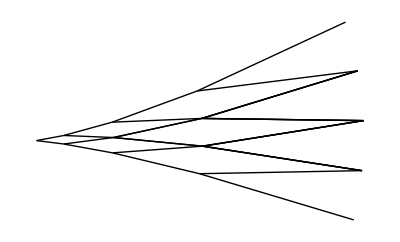

```mathematica
Graphics[Line[ReIm[Catenate[Table[{#[[1]],x},{x,#[[2]]}]&/@nestedPoints]]]]
```